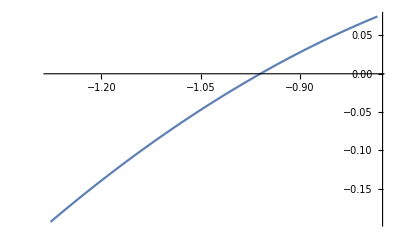

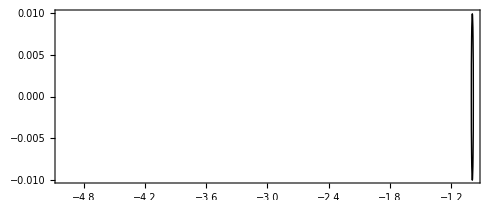

```mathematica
RealPart[W_] := (-4 W^2)/(0.0004 W^4+ 0.00000036 W^6+0.0009 W^4+W^2)
ImPart[W_] := (0.048 W^3-80W)/(0.0004 W^4+ 0.00000036 W^6+0.0009 W^4+W^2)

G1 =ListLinePlot[Table[{RealPart[x],ImPart[x]}, {x, 35, 45, 0.01}], PlotRange->{Automatic, Automatic}]
G2 = Graphics[Circle[{-1,0},0.01], PlotRange->{{-5,-1}, Automatic}, Frame->True, Axes->True]
Show[G1,G2]
```

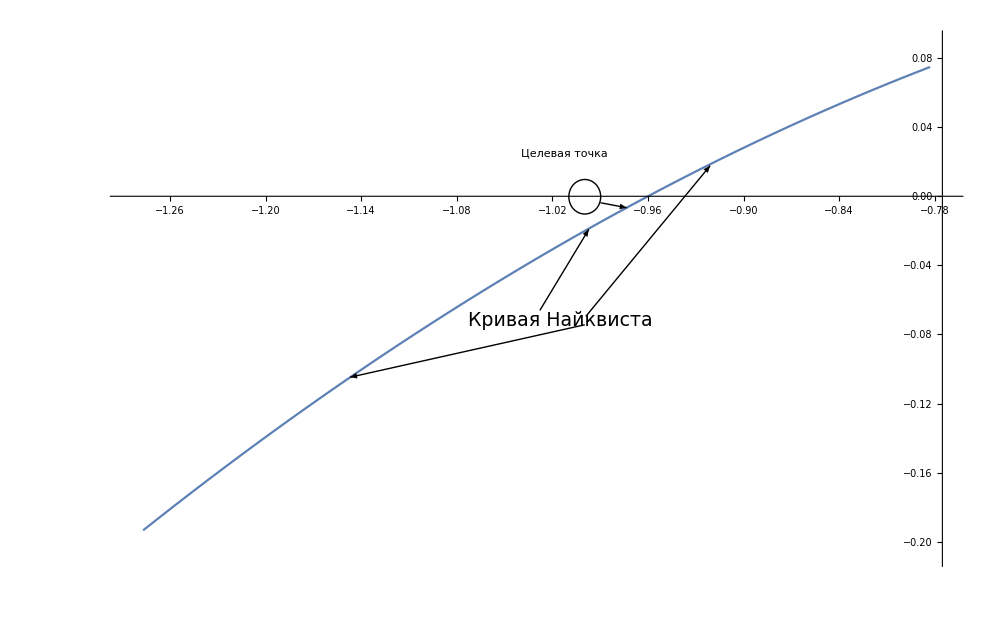

```mathematica
ListLinePlot[ImTable]
```

ListLinePlot::lpn: ImTable is not a list of numbers or pairs of numbers.

ListLinePlot[ImTable]